```mathematica
Clear["Global`*"];
Off[NIntegrate::slwcon];Off[NIntegrate::ncvb];Off[NIntegrate::izero];Off[NIntegrate::oidiv];Off[NIntegrate::errprec];
```

```mathematica
(* If[n==0,1,(1-x)^1(1+x)^n x^0] || (1-x^2)×LegendreP[n,x] *)
```

```mathematica
BasisFunction[n_]:=Function[{x},(1-x^2)×0+LegendreP[n,x]];
BasisMin=0;
BasisMax=10;
Plot[Evaluate[Table[BasisFunction[n][x],{n,BasisMin,BasisMax}]],{x,-1,1},ImageSize->Medium,PlotRange->All];
```

```mathematica
PolinomeToCartesianBasis[y_]:=y.Table[BasisFunction[n][x],{n,BasisMin,BasisMax}];
```

```mathematica
qFunction[x_]=PDF[NormalDistribution[0.1,0.2],x];
q=Table[NIntegrate[qFunction[x]BasisFunction[n][x],{x,-1,1}],{n,BasisMin,BasisMax}];
Plot[{qFunction[x],PolinomeToCartesianBasis[q]},{x,-1,1},PlotRange->All];
```

```mathematica
(* (∂_(x,x) BasisFunction[m][x])×BasisFunction[n][x] *)
```

```mathematica
L=Table[NIntegrate[(D[BasisFunction[m][x], x])×(D[BasisFunction[n][x], x]),{x,-1,1}],{n,BasisMin,BasisMax},{m,BasisMin,BasisMax}];
```

```mathematica
CoordinatesTable = Table[Subscript[c, i],{i,BasisMin,BasisMax}];
Functional = L.CoordinatesTable.CoordinatesTable-2q.CoordinatesTable;
```

```mathematica
left=1;right=1;
findMin=-10;findMax=10;
Coordinates=CoordinatesTable/.NMinimize[{Functional,
(PolinomeToCartesianBasis[CoordinatesTable]/.{x->-1})==left && 
(PolinomeToCartesianBasis[CoordinatesTable]/.{x->1})==right},
CoordinatesTable(*∈Cuboid[Table[findMin,{i,BasisMin,BasisMax}],Table[findMax,{i,BasisMin,BasisMax}]]*)][[2]];
```

```mathematica
AnaliticalSolution=y/.NDSolve[{D[y[x], x,x]==-qFunction[x],y[-1]==left,y[+1]==right},y,{x,-1,1}][[1]];
```

LinearSolve::nosol: Linear equation encountered that has no solution.

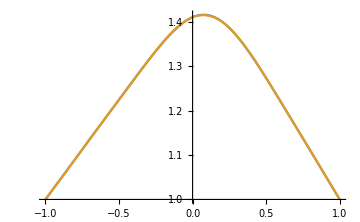

```mathematica
Plot[Evaluate[{AnaliticalSolution[x],PolinomeToCartesianBasis[Coordinates],PolinomeToCartesianBasis[LinearSolve[L,q]]}],{x,-1,1},ImageSize->Medium]
```

```mathematica
{D[PolinomeToCartesianBasis[Coordinates],x]/.{x->-1},D[PolinomeToCartesianBasis[Coordinates],x]/.{x->+1}};
```